## AOM and lock settings

We lock to F=1->F’=2 on the D1 line.

```mathematica
F1toF2=816.65(*5P1/2 hyperfine splitting, i.e. the amount to cancel with the AOMs to get to F=1->F'=1 resonance*)
-92.65+2(-362)
```

816.65

-816.65

## estimate of sensitivity to quantization axis

From https://wiki.physics.wisc.edu/saffmanwiki/ResearchProjects/RubidiumExperiment/D1OP MFE 5.10.2016, given the depumping curves vs shim coils, we can deduce what the angular sensitivity is and figure out how far we need to scan given our coils

```mathematica
dIX=0.15;(*~FWHM of current*)
dIY=0.15;(*~FWHM of current*)
BXGperA=2.03;
BZGperA=9;
Bbias=3.7;(*guess based on Fig. 6.2 of Minho's thesis*)
"angular sensitivity to optimized depump"
ArcTan[3.7,dIX*BXGperA/2]
```

angular sensitivity to optimized depump

0.0411254

```mathematica
gain=0.228;(*coil driver gain, A/V*)
GperAmpZ=8.75;
GperAmpXY=2.27;
AZbottomV=0;
AZtopV= 0;
BZ= gain GperAmpZ(AZbottomV-AZtopV) ;
BX=gain GperAmpXY AXV;
BY =gain GperAmpXY AYV;
"angle scanned X"
ArcTan[1,gain GperAmpXY *0.1]
"angle scanned Z"
ArcTan[1,gain GperAmpZ *0.025]
```

angle scanned X

0.0517099

angle scanned Z

0.0498337

## estimates of B field at atoms

```mathematica
gain=0.228;(*coil driver gain, A/V*)
GperAmpZ=8.75;
GperAmpXY=2.27;
AZbottomV=0;
AZtopV= 0;
AXV=0;
AYV=-6.2;
BZ= gain GperAmpZ(AZbottomV-AZtopV) ;
BX=gain GperAmpXY AXV;
BY =gain GperAmpXY AYV;
"B(Gauss) at atoms"
√(BX^2+BY^2+BZ^2)
```

B(Gauss) at atoms

3.20887

```mathematica
gain=0.228;(*coil driver gain, A/V*)
GperAmpZ=8.75;
GperAmpXY=2.27;
AZbottomV=0;
AZtopV= 0;
AXV=0;
AYV=2;
BZ= gain GperAmpZ(AZbottomV-AZtopV) ;
BX=gain GperAmpXY AXV;
BY =gain GperAmpXY AYV;
"B(Gauss) at atoms"
√(BX^2+BY^2+BZ^2)
```

B(Gauss) at atoms

1.03512

magnetic field at the atoms (optical pumping, 2024.05.20)

```mathematica
gain=0.228;(*coil driver gain, A/V*)
GperAmpZ=8.75;
GperAmpXY=2.27;
AZbottomV=-0.102;
AZtopV= -0.244;
AXV=0.14;
AYV=-6.2;
BZ= gain GperAmpZ(AZbottomV-AZtopV) ;
BX=gain GperAmpXY AXV;
BY =gain GperAmpXY AYV;
"B(Gauss) at atoms"
√(BX^2+BY^2+BZ^2)
```

B(Gauss) at atoms

3.22217

magnetic field at the atoms (optical pumping, 2024.05 .30)

```mathematica
gain=0.228;(*coil driver gain, A/V*)
GperAmpZ=8.75;
GperAmpXY=2.27;
AZbottomV=-0.172;
AZtopV= 0.078;
AXV=-0.662;
AYV=-6.2;
BZ= gain GperAmpZ(AZbottomV-AZtopV) ;
BX=gain GperAmpXY AXV;
BY =gain GperAmpXY AYV;
"BX,BY,BZ"
{BX,BY,BZ}
"B(Gauss) at atoms"
√(BX^2+BY^2+BZ^2)
```

BX,BY,BZ

{-0.342625,-3.20887,-0.49875}

B(Gauss) at atoms

3.26543

```mathematica
gain=0.228;(*coil driver gain, A/V*)
GperAmpZ=8.75;
GperAmpXY=2.27;
AZbottomV=-0.172;
AZtopV= 0.078;
AXV=-0.2;
AYV=-9.6;
BZ= gain GperAmpZ(AZbottomV-AZtopV) ;
BX=gain GperAmpXY AXV;
BY =gain GperAmpXY AYV;
"BX,BY,BZ"
{BX,BY,BZ}
"B(Gauss) at atoms"
√(BX^2+BY^2+BZ^2)
```

BX,BY,BZ

{-0.103512,-4.96858,-0.49875}

B(Gauss) at atoms

4.99462

```mathematica
ArcTan[3,0.1]
```

0.033321

```mathematica
gain GperAmpXY 1
```

0.51756

```mathematica
ArcTan[Abs[BY],√(2 bx^2)] 180/π/.bx->0
```

0.

```mathematica
gain GperAmpZ 0.25
```

0.49875

```mathematica
1/20//N
```

0.05

```mathematica
ArcTan[0]
```

0

```mathematica
BY
```

-3.20887

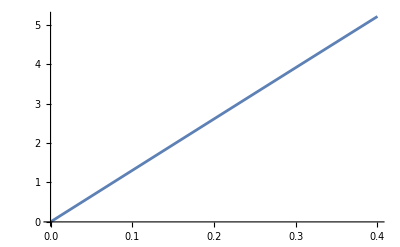

```mathematica
Plot[{ArcTan[Abs[BY],√((gain GperAmpZ aV)^2+(gain GperAmpXY aV)^2)] 180/π,ArcTan[Abs[BY],√(2( gain GperAmpZ)^2)] 180/π},{aV,0,0.4}]
```

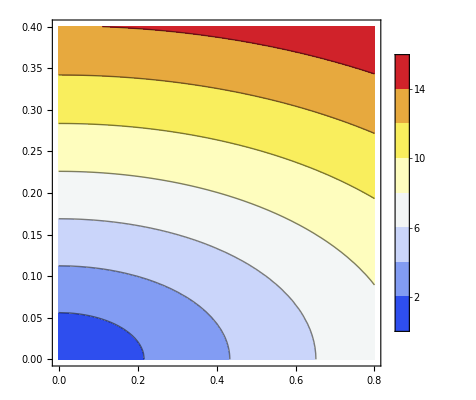

```mathematica
ContourPlot[ArcTan[Abs[BY],√((gain GperAmpZ azV)^2+(gain GperAmpXY axV)^2)] 180/π,{axV,0,0.8},{azV,0,0.4},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

FORT polarization sensitivity. the prefactor in the second plot is the TTI voltage range at setpoint to off

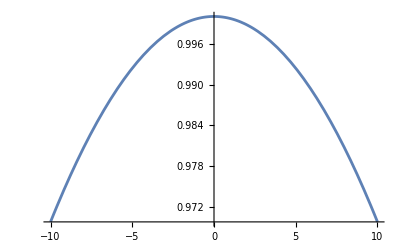

```mathematica
Plot[Cos[π/180 deg]^2,{deg,-10,10}]
```

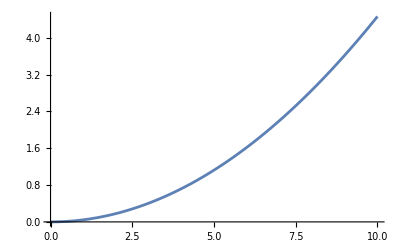

```mathematica
Plot[(224-76)(1-Cos[π/180 deg]^2),{deg,0,10}]
```

```mathematica
1e4*35e-6
```

-6+35 e e4

```mathematica
Integrate[Exp[-t^2/(2 T^2)],{t,-∞,∞}]
```

ConditionalExpression[(√(2 π))/(√(1/T^2)), Re[T^2]>0]

```mathematica
2 √(π Log[2.])
```

2.95133

```mathematica
2(√(π Log[2.]))/π
```

0.939437

```mathematica
0.5 √(π /Log[2.])
```

1.06447

```mathematica
(1.06)^2
```

1.1236

Urukul clock calcs. https://m-labs.hk/artiq/manual/core_drivers_reference.html?highlight=sync_device

```mathematica
plln=32;(*40 default*)
fref=125*^6;(*set in parent CPLD*)
clkdiv=4;(*4 is default for AD9910. set in parent CPLD*)
pllvco=5;(*5 default*)
DDSsampleclk=plln*fref/clkdiv
```

1000000000

What if we use a 10 MHz reference?

```mathematica
plln=100;(*40 default*)
fref=10*^6;(*set in parent CPLD*)
clkdiv=1;(*4 is default for AD9910. set in parent CPLD*)
pllvco=5;(*5 default*)
DDSsampleclk=plln*fref/clkdiv
```

1000000000

```mathematica
sysclk=DDSsampleclk;
sysclk*(1*^-6)
```

1000

sysclk = 1000 means we need pll_vco=5, which is the default.

AOMs for D1 OP

```mathematica
-372*2+80-150.5
```

-814.5

```mathematica
-362*2+-90
```

-814

```mathematica
-372*2+80-150.5
```

```mathematica
-372*2+80
```

```mathematica
-664/2
```

-332

```mathematica
0.7^2/0.88^2
```

0.632748

```mathematica
1/(2π √(20*^3*10^-6))//N
```

1.1254

## TTI monitor curve

```mathematica
1/(√200)//N
```

0.0707107

```mathematica
-92.65+2(-362)=-816.65
```

-816.65

```mathematica
data={{30.7,136},{48.5,412}};
line = Fit[data, {1,x},x]
```

-340.022+15.5056 x

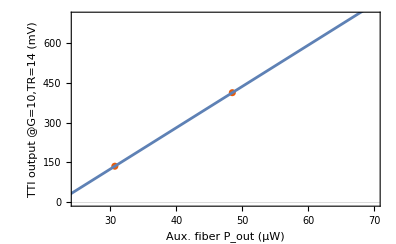

```mathematica
Show[ListPlot[data,PlotTheme->"Scientific",FrameLabel->{"Aux. fiber P_out (μW)","TTI output @G=10,TR=14 (mV)"},LabelStyle->Directive[Black,FontSize->12]],Plot[line,{x,10,70}],PlotRange->{{25,70},{0,700}}]
```

```mathematica
Solve[-150.5-2(x)==-814,x]
```

{{x→331.75}}